WolframAlphaQueryResults

78.6902 yr

```mathematica
CountryData["UnitedStates","LifeExpectancy"]
```

78.6902 yr

```mathematica
data = DeleteCases[
Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData[All]}],{_,_Missing}];
Short[data]
```

{{Afghanistan,63.673 yr},{Albania,78.345 yr},{Algeria,76.078 yr},{American Samoa,73.72 yr},{Andorra,82.51 yr},{Angola,61.547 yr},{Anguilla,80.65 yr},{Antigua and Barbuda,76.364 yr},{Argentina,76.577 yr},{Armenia,74.618 yr},{Aruba,75.867 yr},{Australia,82.5 yr},{Austria,80.8902 yr},{Azerbaijan,72.026 yr},«204»,{United Kingdom,80.9561 yr},{United States,78.6902 yr},{United States Virgin Islands,79.2683 yr},{Uruguay,77.493 yr},{Uzbekistan,71.314 yr},{Vanuatu,72.133 yr},{Venezuela,74.545 yr},{Vietnam,76.253 yr},{Wallis and Futuna Islands,78.2 yr},{West Bank,74.54 yr},{Western Sahara,67.764 yr},{Yemen,64.953 yr},{Zambia,61.874 yr},{Zimbabwe,61.163 yr}}

```mathematica
Short[SortBy[data,Last]]
```

{{Sierra Leone,51.835 yr},{Central African Republic,52.171 yr},{Chad,52.903 yr},{Nigeria,53.428 yr},{Ivory Coast,53.582 yr},{Lesotho,54.174 yr},{Somalia,56.293 yr},{South Sudan,56.811 yr},{Guinea-Bissau,57.403 yr},{Burundi,57.481 yr},{Equatorial Guinea,57.681 yr},{Eswatini,57.754 yr},{Mali,57.966 yr},{Cameroon,58.073 yr},«204»,{Canada,82.3005 yr},{Iceland,82.4683 yr},{Australia,82.5 yr},{Norway,82.5098 yr},{Andorra,82.51 yr},{Italy,82.5439 yr},{Liechtenstein,82.6561 yr},{Singapore,82.7951 yr},{Spain,82.8317 yr},{Switzerland,82.8976 yr},{Macau,83.849 yr},{Japan,83.9849 yr},{Hong Kong,84.2268 yr},{San Marino,85.4171 yr}}

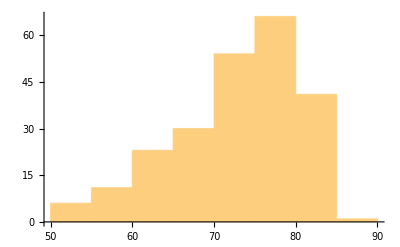

```mathematica
Histogram[data⟦All,2⟧]
```

```mathematica
dataAfrica = DeleteCases[
Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Africa"]}],{_,_Missing}];
Mean[dataAfrica⟦All,2⟧]
```

63.7301 yr

```mathematica
dataAsia = DeleteCases[
Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Asia"]}],{_,_Missing}];
Mean[dataAsia⟦All,2⟧]
```

73.6869 yr

```mathematica
dataEuro = DeleteCases[
Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Europe"]}],{_,_Missing}];
Mean[dataEuro⟦All,2⟧]
```

79.1589 yr

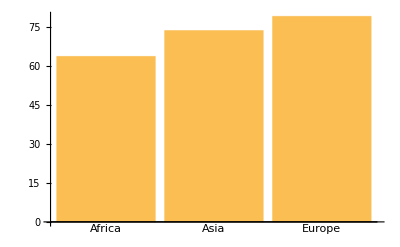

```mathematica
BarChart[{Mean[dataAfrica⟦All,2⟧],Mean[dataAsia⟦All,2⟧],Mean[dataEuro⟦All,2⟧]},
ChartLabels-> {"Africa","Asia","Europe"}]
```

```mathematica
Take[dataAsia,3]
```

{{Afghanistan,63.673 yr},{Armenia,74.618 yr},{Azerbaijan,72.026 yr}}

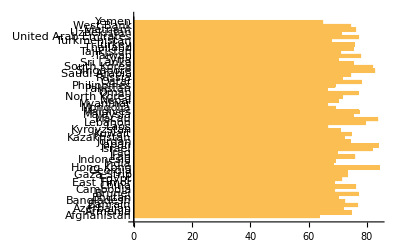

```mathematica
BarChart[dataAsia⟦All,2⟧,ChartLabels->dataAsia⟦All,1⟧,
BarOrigin->Left]
```

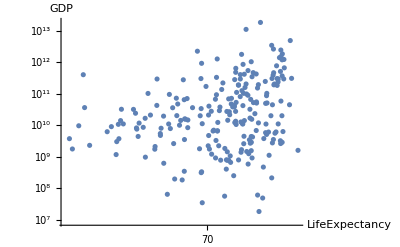

```mathematica
data = Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"GDP"]},
CountryData[i,"Name"]],{i,CountryData[]}];
ListLogLogPlot[data,AxesLabel->{"LifeExpectancy","GDP"}]
```

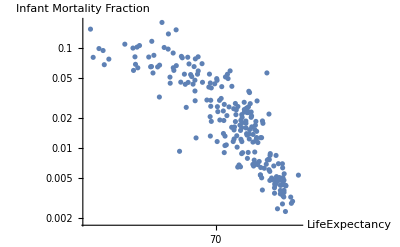

```mathematica
data = Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"InfantMortalityFraction"]},
CountryData[i,"Name"]],{i,CountryData[]}];
ListLogLogPlot[data,AxesLabel->{"LifeExpectancy","Infant Mortality Fraction"}]
```

```mathematica
Manipulate[
plotFn[Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,prop]},
CountryData[i,"Name"]],{i,CountryData[]}],
AxesLabel-> {"Life Expectancy",prop}],
{prop,{"InfantMortalityFraction","GDP","LiteracyFraction"}},
{{plotFn,ListLogLogPlot},{ListPlot,ListLogPlot,ListLogLogPlot}},
SaveDefinitions->True]
```